```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

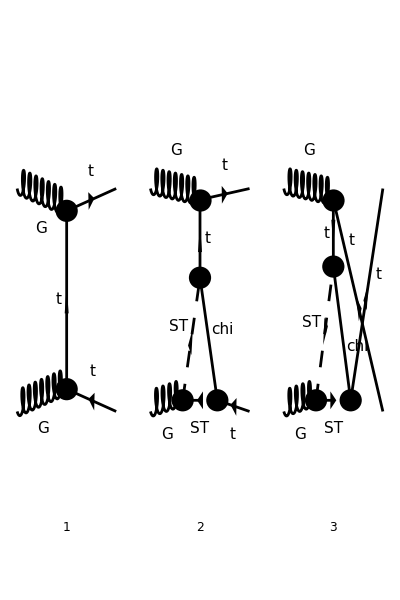

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
goodDiags=DiagramExtract[goodDiags,{2,6,8}];
(* goodDiags=DiagramExtract[goodDiags,{1,5}]; *)
(* goodDiags=DiagramExtract[goodDiags,{4, 10,11}]; *)
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 400,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},TransversePolarizationVectors->{k1,k2}, LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames->{μ,ν}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]];
(* Remove terms of higher order *)
ampB = Normal[Series[ampB,{yDM,0,2},{gs,0,2}]];
```

in total: 3 Particles amplitudes

```mathematica
ampC =Simplify[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])];
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampD=Simplify[ampC-ampSM];
(* ampD=ampD/.{PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C00,PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C11,PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C12,PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C1}; *)
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DiracSimplify[ampD]];
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp,PaVe]]}]
```

(C_2(0,t,MT^2,mST^2,mST^2,mChi^2) | 0
C_2(0,u,MT^2,mST^2,mST^2,mChi^2) | 0
C_00(0,t,MT^2,mST^2,mST^2,mChi^2) | 1/(4 ε_UV)
C_00(0,u,MT^2,mST^2,mST^2,mChi^2) | 1/(4 ε_UV)
C_12(0,t,MT^2,mST^2,mST^2,mChi^2) | 0
C_12(0,u,MT^2,mST^2,mST^2,mChi^2) | 0
C_22(0,t,MT^2,mST^2,mST^2,mChi^2) | 0
C_22(0,u,MT^2,mST^2,mST^2,mChi^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp,deltaCTR]] (-1/(4 EpsilonUV));
FullSimplify[loopUV+ctUV]
```

-1/(2 ε_UV)ⅈ π^2 gs^2 yDM^2 (((T^Glu1 T^Glu2)_Col3Col4 ((φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT))-2 (p2·ε(k2)) (φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))))/((k2-p2)^2-MT^2)+1/((k2-p1)^2-MT^2)(T^Glu2 T^Glu1)_Col3Col4 (-2 (p1·ε(k2)) (φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))+MT (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))-MT (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT))+(φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))))

## Tensor Structure

```mathematica
PVsubs =Flatten[Table[PaVe[a,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a],ToString[b]]],{a,0,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[b]]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],ToString[b]]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
```

```mathematica
ampEsimp2=DiracSimplify[ampEsimp/.{DiracGamma[7]->1-DiracGamma[6]}];
```

```mathematica
spinorChains=Sort[Tally[Cases[ampEsimp2,Spinor[___].___.Spinor[___],All]][[All,1]]]
pairs=Cases2[ampEsimp2,Pair]
gammas=Cases2[ampEsimp2,DiracGamma]
allTerms=Sort[Join[spinorChains,gammas]];
```

{(φ(p1,MT)).(γ·ε(k1)).(φ(-p2,MT)),(φ(p1,MT)).(γ·k2).(γ·ε(k1)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT)),(φ(p1,MT)).(γ·k2).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))}

{p1·ε(k2),p2·ε(k2)}

{(γ̄)^6,γ·k2,γ·ε(k1),γ·ε(k2)}

### Coefficients for each term

```mathematica
Table[{allTerms[[i]],FullSimplify[Coefficient[ampEsimp2,allTerms[[i]]]]},{i,1,Length[allTerms]}]
```

((γ̄)^6 | 0
γ·k2 | 0
γ·ε(k1) | 0
γ·ε(k2) | 0
(φ(p1,MT)).(γ·ε(k1)).(φ(-p2,MT)) | -2 ⅈ π^2 gs^2 yDM^2 (((p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (MT^2 (C_2(0,t,MT^2,mST^2,mST^2,mChi^2)+C_22(0,t,MT^2,mST^2,mST^2,mChi^2))+4 deltaCTL))/((k2-p2)^2-MT^2)-(MT^2 (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4 (C_2(0,u,MT^2,mST^2,mST^2,mChi^2)+C_22(0,u,MT^2,mST^2,mST^2,mChi^2)))/((k2-p1)^2-MT^2))
(φ(p1,MT)).(γ·k2).(γ·ε(k1)).(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4 C_12(0,u,MT^2,mST^2,mST^2,mChi^2))/((k2-p1)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) | (ⅈ π^2 gs^2 yDM^2 ((u (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 ((mChi^2-mST^2-t) B_0(t,mChi^2,mST^2)+2 t ((-mChi^2+mST^2+MT^2) C_2(0,t,MT^2,mST^2,mST^2,mChi^2)+2 MT^2 C_22(0,t,MT^2,mST^2,mST^2,mChi^2)+4 deltaCTL-4 deltaCTR)-A_0(mChi^2)+A_0(mST^2)))/((k2-p2)^2-MT^2)+(t (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4 ((-mChi^2+mST^2+u) B_0(u,mChi^2,mST^2)+2 u (mChi^2-mST^2-MT^2) C_2(0,u,MT^2,mST^2,mST^2,mChi^2)-4 MT^2 u C_22(0,u,MT^2,mST^2,mST^2,mChi^2)+A_0(mChi^2)-A_0(mST^2)))/((k2-p1)^2-MT^2)))/(t u)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 MT yDM^2 (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (C_12(0,t,MT^2,mST^2,mST^2,mChi^2)+C_2(0,t,MT^2,mST^2,mST^2,mChi^2)+C_22(0,t,MT^2,mST^2,mST^2,mChi^2)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (-C_00(0,t,MT^2,mST^2,mST^2,mChi^2)+deltaCTL-deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (T^Glu2 T^Glu1)_Col3Col4 C_00(0,u,MT^2,mST^2,mST^2,mChi^2))/((k2-p1)^2-MT^2)
(φ(p1,MT)).(γ·k2).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 MT yDM^2 (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4 (2 C_12(0,u,MT^2,mST^2,mST^2,mChi^2)+C_2(0,u,MT^2,mST^2,mST^2,mChi^2)+C_22(0,u,MT^2,mST^2,mST^2,mChi^2)))/((k2-p1)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) | (2 ⅈ π^2 gs^2 MT yDM^2 (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4 (2 C_12(0,t,MT^2,mST^2,mST^2,mChi^2)+C_2(0,t,MT^2,mST^2,mST^2,mChi^2)+C_22(0,t,MT^2,mST^2,mST^2,mChi^2)))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)) | (4 ⅈ π^2 deltaCTL gs^2 yDM^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | -(4 ⅈ π^2 gs^2 MT yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (-C_00(0,t,MT^2,mST^2,mST^2,mChi^2)+deltaCTL-deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) | -(4 ⅈ π^2 gs^2 MT yDM^2 (T^Glu2 T^Glu1)_Col3Col4 C_00(0,u,MT^2,mST^2,mST^2,mChi^2))/((k2-p1)^2-MT^2)
(φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 yDM^2 (T^Glu1 T^Glu2)_Col3Col4 (-C_00(0,t,MT^2,mST^2,mST^2,mChi^2)+2 deltaCTL-2 deltaCTR))/((k2-p2)^2-MT^2)
(φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) | -(2 ⅈ π^2 gs^2 yDM^2 (T^Glu2 T^Glu1)_Col3Col4 C_00(0,u,MT^2,mST^2,mST^2,mChi^2))/((k2-p1)^2-MT^2))